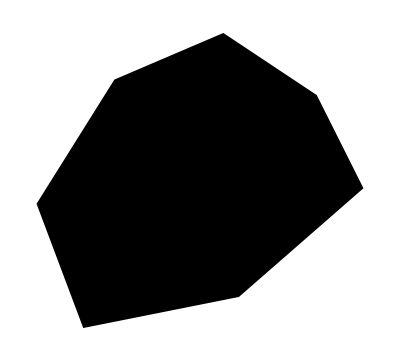

```mathematica
pts = {{0,0},{10,2},{18, 9}, {15, 15},{9, 19},{2, 16}, {-3, 8}};
Graphics[Polygon[pts]]
```

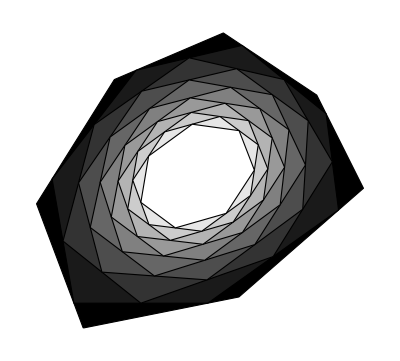

```mathematica
Graphics[makepolygons[pts,10, 5]]
```

```mathematica
GetMidPoints[list_,idx_, s_]:=
Module[{r={}},
If[idx==0,Return[list],Null];
For[j=1,j<Length[list],j++,AppendTo[r,(list[[j]]+(s-1)list[[j+1]])/s]];
AppendTo[r,(list[[Length[list]]]+(s-1)list[[1]])/s];
If[idx==1,Return[r],Return[GetMidPoints[r,idx-1]]]
]
```

```mathematica
makepolygons[pts_,depth_, s_]:=
Module[{graph={}},
For[i=0,i≤depth,i++,{AppendTo[graph,RGBColor[N[i/depth],N[i/depth],N[i/depth]]],
AppendTo[graph,EdgeForm[{Thin,Black}]],
AppendTo[graph,Polygon[GetMidPoints[pts,i, s]]]}];
Return[graph]
]
```

```mathematica
GetMidPoints[pts,4]
```

{{217/16,141/16},{105/8,55/4},{137/16,255/16},{51/16,219/16},{9/16,133/16},{3,65/16},{9,71/16}}

```mathematica
makepolygons[pts,5]
```

0

1

2

3

4

5

{RGBColor[0., 0., 0.],RGBColor[0.2, 0.2, 0.2],RGBColor[0.4, 0.4, 0.4],RGBColor[0.6, 0.6, 0.6],RGBColor[0.8, 0.8, 0.8],RGBColor[1., 1., 1.]}

{RGBColor[0., 0., 0.],RGBColor[0.2, 0.2, 0.2],RGBColor[0.4, 0.4, 0.4],RGBColor[0.6, 0.6, 0.6],RGBColor[0.8, 0.8, 0.8],RGBColor[1., 1., 1.]}

```mathematica
genrandompolypoints[n_]:=
Module[{r=10,result={}},
rands=Sort[RandomReal[2Pi,{n}]];
Return[Table[{r*Sin[rands[[k]]],r*Cos[rands[[k]]]},{k,n}]];
]
```

```mathematica
genrandompolypoints[10]
```

{{-9.96368,0.851481},{-9.90441,1.3794},{7.60302,-6.4957},{7.39912,-6.72704},{6.29489,-7.7701},{0.098564,-9.99951},{0.0570804,-9.99984},{7.21514,6.924},{-7.40882,-6.71635},{7.65157,6.43844}}

```mathematica
rands=RandomReal[2Pi,{10}]
```

{4.35962,2.47368,2.29216,5.66352,1.68877,3.49959,5.87413,0.457489,3.47847,2.77669}

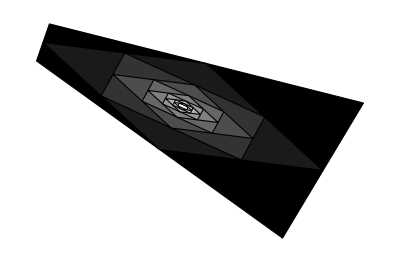
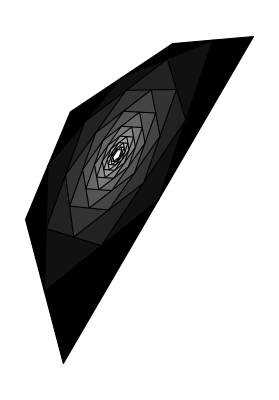
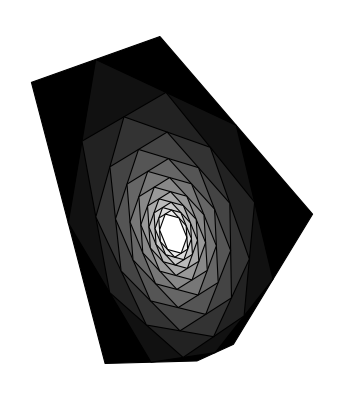
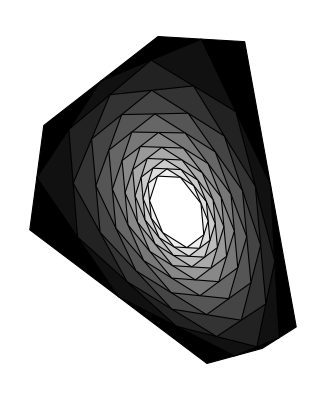
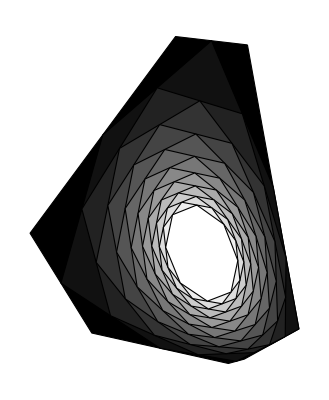
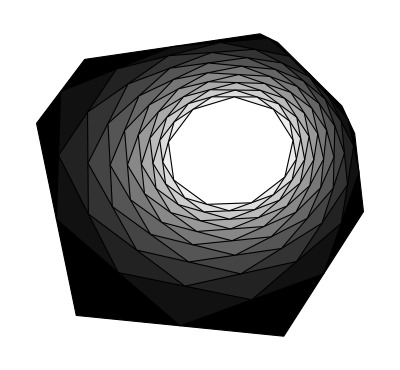

```mathematica
{Graphics[makepolygons[genrandompolypoints[4],10]],
Graphics[makepolygons[genrandompolypoints[5],15]],
Graphics[makepolygons[genrandompolypoints[6],15]],
Graphics[makepolygons[genrandompolypoints[7],15]],
Graphics[makepolygons[genrandompolypoints[8],15]],
Graphics[makepolygons[genrandompolypoints[9],15]]}
```